## Optimal Execution with Limit and Market Orders

## 8.2 Liquidation with Only Limit Orders

```mathematica
ω[t_,q_]:= ∑_(n=0)^q tλ^n/(n!)*ⅇ^(-κ*α*(q-n)^2)*(T-t)^n
ω[t_,q_]:=ⅇ^(-κ*α*q^2)/;t==T
ω[t_,q_]:=1/;q== 0
```

```mathematica
δ[t_,q_]:=1/κ*(1+Log[ω[t,q]/ω[t,q-1]])
(*
	Optimal Depth: Post LO @Price=S_t + δ 
*)
```

```mathematica
λ=50/60;
tλ=λ*ⅇ^-1;

κ=100.0;
T=60;
α=10^-3;
𝒩=5;
σ=0.01;
```

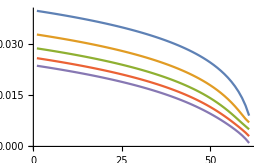

```mathematica
ListLinePlot@Table[Table[N@δ[t,q],{t,0,T}],{q,1,5}](*α-> 10^-3*)
```

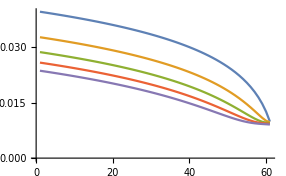

```mathematica
ListLinePlot@Table[Table[N@δ[t,q],{t,0,T}],{q,1,5}](*α-> 10^-4*)
```

#### Numerical Experiments

```mathematica
(*Price Dynamics*)
S0=30;
𝒫=TransformedProcess[S0+σ*(W[t]),{W\[Distributed]WienerProcess[]},t];
TWAP[price_]:=MovingMap[Mean,price,price["PathLength"],None]
```

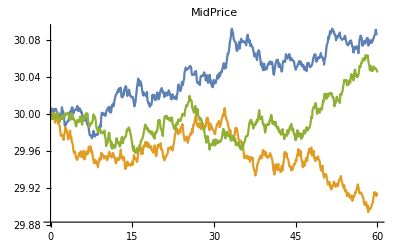
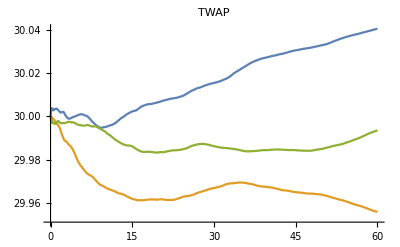

```mathematica
With[{data = RandomFunction[𝒫,{0,T,0.1},3]},
{ListLinePlot[data,PlotRange->All,PlotLabel->"MidPrice"], ListLinePlot[TWAP[data],PlotLabel->"TWAP"]}]
```

```mathematica
fillProb[δ_]:=ⅇ^(-κ*δ)
```

```mathematica
fillProb[0.01]
```

0.367879

```mathematica
backTest[price_]:=Module[
{left=𝒩,
tb=Normal[price][[1]],
depth,
time,
mPrice,
postPrice,
fillQ,
depthHis={},
inventoryHis={},
trdHis={},
priceHis={},
MOs=0},

Do[
{
AppendTo[priceHis,tb[[idx]]];
time=tb[[idx]][[1]];
mPrice=tb[[idx]][[2]];
depth=δ[time,left];
AppendTo[depthHis,{time,depth}];
If[left>0,postPrice=mPrice+depth;
fillQ=RandomVariate[BernoulliDistribution[fillProb[depth]]];
If[fillQ==1,AppendTo[trdHis,{time,postPrice}]];
left-=fillQ;];
AppendTo[inventoryHis,{time,left}];
};
If[left>0&&idx== Length@tb,
AppendTo[inventoryHis,{tb[[idx]][[1]], 0}];AppendTo[trdHis,{tb[[idx]][[1]],tb[[idx]][[2]]}];MOs=left;left=0;];
If[left==0,Break[]];,
{idx,1,Length@tb}];
Association[
"depth"-> TemporalData[depthHis],
"inventory"-> TemporalData[inventoryHis],
"trade"-> TemporalData[trdHis],
"price"-> TemporalData[priceHis],
"MOs"-> MOs]
]
```

<|depth→TemporalData[…],inventory→TemporalData[…],trade→TemporalData[…],price→TemporalData[…],MOs→0|>

ListLinePlot::lpn: 0. is not a list of numbers or pairs of numbers.

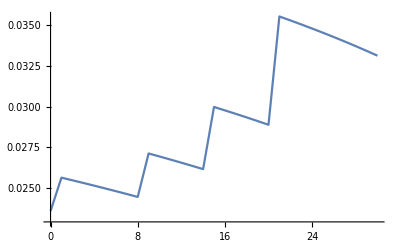
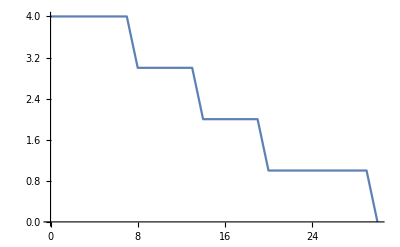
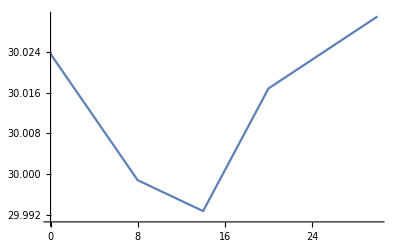
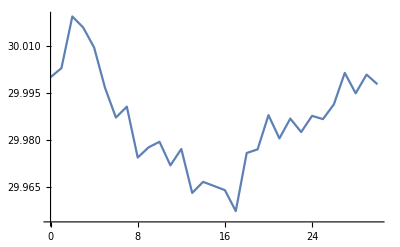
<|depth→-Graphics-,inventory→-Graphics-,trade→-Graphics-,price→-Graphics-,MOs→ListLinePlot[0]|>

```mathematica
dt = RandomFunction[𝒫,{0,T-1,1},1];
res=backTest[dt]
Map[ListLinePlot,res]
```

## 8.4 Liquidation with Limit and Market Orders

```mathematica
Clear["Global`*"]
```

```mathematica
ξ=0.005;(*half spread*)
T=60;
𝒩=10;
λ=50/60;
tλ=λ*ⅇ^-1;
κ=100;
S0=30;
σ=0.01;
α=0.001;
ϕ=10^-4;

𝒫=TransformedProcess[S0+σ*(W[t]),{W\[Distributed]WienerProcess[]},t];
```

```mathematica
(*terminal liquidation penalty*)
ℓ[q_]:=q*(ξ+α*q)
```

```mathematica
ω[t_,q_]:=ⅇ^(-κ*q*(ξ+α*q))/;t== T&&1≤ q≤ 𝒩
```

```mathematica
ω[t_,q_]:=1/; q==0
```

```mathematica
Table[ω[T,i],{i,0,𝒩}]
```

{1,0.548812,0.246597,0.090718,0.0273237,0.00673795,0.00136037,0.000224867,0.0000304325,3.37202×10^-6,3.05902×10^-7}

```mathematica
Thread[ⅇ^(-κ*ξ)*Table[ω[T,i],{i,𝒩}][[1;;-2]]-Table[ω[T,i],{i,𝒩}][[2;;]]≤ 0]
```

{False,False,False,False,False,False,False,False,False}

```mathematica
fdmSolve[t_,q_]:=Module[
{totalInv=q,
totalT=t,
times=Reverse@N@Subdivide[0,t,1000-1],
Tvals=Table[ω[T,i],{i,0,q}],
zeroInvVals=Map[ω[#,0]&,Reverse@N@Subdivide[0,t,1000-1]],
curT,prvT,
timeStep=First@Differences@Reverse@N@Subdivide[0,t,1000-1],
curQ,prvQ},
Table[
curQ=If[idxQ==0,zeroInvVals,
Table[
curT=If[times[[idxT]]== t,ω[times[[idxT]],idxQ],N[(prvT+tλ*timeStep*prvQ[[idxT]])/(1+κ*ϕ*timeStep*idxQ^2)]];(* ω[t,q] should be
ⅇ^-κξ ω[t,q-1]-ω[t,q]≤0
∂_t ω[t,q]-κϕq^2 ω[t,q]+λ̃ ω[t,q-1]≤ 0

when ⅇ^-κξ ω[t,q-1]-ω[t,q]< 0, ∂_t ω[t,q]-κϕq^2 ω[t,q]+λ̃ ω[t,q-1]== 0;
   when ⅇ^-κξ ω[t,q-1]-ω[t,q]==0, ω[t,q]=ⅇ^-κξ ω[t,q-1] and ∂_t ω[t,q]-κϕq^2 ω[t,q]+λ̃ ω[t,q-1] < 0;
   when ⅇ^-κξ ω[t,q-1]-ω[t,q>0, this is .... 
*)
If[ⅇ^(-κ*ξ)*prvQ[[idxT]]-curT≤ 0,{},curT= ⅇ^(-κ*ξ)*prvQ[[idxT]]];
If[(prvT-curT)/timeStep-κ*ϕ*idxQ^2*curT+tλ*prvQ[[idxT]]≤ 0,{},{}];
prvT=curT;
curT,{idxT,1,Length@times}]
];
prvQ=curQ;
Echo[curQ];
curQ
,{idxQ,0,q}]
]
```

```mathematica
mat
```

{1}
 |  |  |  |

```mathematica
Dimensions@mat
```

{11,1000}

```mathematica
sol=Reverse[mat,2]
```

{1}
 |  |  |  |

```mathematica
sol
```